# 圆锥曲线

### 垂直截面

```mathematica
Manipulate[Graphics3D[{EdgeForm[Magenta],Cone[],Cone[{{0,0,3},{0,0,1}}]},PlotRange->{{-1,1},{-y,1},{-0.95,2.95}}],{{y,0.33},-1,1}]
```

不难发现截线是双曲线

### 在进一步展现其他情况之前，先解决一个问题

根据定点P和法线向量v，计算无限大平面

```mathematica
p={px,py,pz};v={v1,v2,v3};
p2={px+1,py+1,zz};
sol=Solve[(p2-p).v==0,zz][[1]]
```

{zz→(-v1-v2+pz v3)/v3}

```mathematica
p2=p2/.sol
```

{1+px,1+py,(-v1-v2+pz v3)/v3}

```mathematica
p3=p+(p2-p)×v
```

{px+(v1 v2)/v3+v2^2/v3+v3,py-v1^2/v3-(v1 v2)/v3-v3,pz-v1+v2}

现在我们得到了过p点、法向量为v的平面上的三个点，p，p2，p3

绘制出来看看效果

```mathematica
DynamicModule[{p,p2,p3,v},Manipulate[p={px,py,pz};v={v1,v2,v3};p2={1+px,1+py,(-v1-v2+pz v3)/v3};p3={px+(v1 v2)/v3+v2^2/v3+v3,py-v1^2/v3-(v1 v2)/v3-v3,pz-v1+v2};Graphics3D[{{Opacity[0.8],InfinitePlane[{p,p2,p3}]},{Thick,Red,Arrow[{p,p+Normalize@v},0.1]},Arrow[{p,p+Normalize[p2-p]},0.1],Arrow[{p,p+Normalize[p3-p]},0.1],Magenta,PointSize[Large],Point[p]},PlotRange->2],{px,-1,1},{py,-1,1},{pz,-1,1},{v1,-1,1},{v2,-1,1},{v3,-1,1}]]
```

### 现在，我们让这个平面去截圆锥面

```mathematica
DynamicModule[{p,p2,p3,v},Manipulate[p={px,py,pz};v={v1,v2,v3};p2={1+px,1+py,(-v1-v2+pz v3)/v3};p3={px+(v1 v2)/v3+v2^2/v3+v3,py-v1^2/v3-(v1 v2)/v3-v3,pz-v1+v2};Graphics3D[{Style[{Cone[],Cone[{{0,0,3},{0,0,1}}]},ClipPlanes->InfinitePlane[{p,p2,p3}],ClipPlanesStyle->{Directive[Opacity[0.3],Green]}],{Thick,Red,Arrow[{p,p+Normalize@v},0.1]},{Magenta,PointSize[Large],Point[p]}},Boxed->False,PlotRange->{{-2,2},{-2,2},{-0.9,2.9}}],{{px,0.5},-1,1},{{py,-0.5},-1,1},{{pz,0},-1,1},{{v1,1},-1,1},{{v2,0},-1,1},{{v3,0.05},-1,1}]]
```

### 优化

现在我们回头看下p2的值{1+px,1+py,(-v1-v2+pz v3)/v3}

这里v3作为分母是不能为0的。

如果假设v3=0，那么平面就会平行于z轴，这时不一定会过点p2

因此，当v3 = 0 时，我们可以推导出这样的p2和p3

p = {px, py, pz}; v = {v1, v2, 0};
p2 = {px, py, pz + 1};
p3 = p + {-v2, v1, 0};

#### 稍微修改前面的栗子

```mathematica
DynamicModule[{p,p2,p3,v},Manipulate[p={px,py,pz};v={v1,v2,v3};p2=If[v3==0,{px, py, pz + 1},{1+px,1+py,(-v1-v2+pz v3)/v3}];p3=If[v3==0,p + {-v2, v1, 0},{px+(v1 v2)/v3+v2^2/v3+v3,py-v1^2/v3-(v1 v2)/v3-v3,pz-v1+v2}];Graphics3D[{Style[{Cone[],Cone[{{0,0,3},{0,0,1}}]},ClipPlanes->InfinitePlane[{p,p2,p3}],ClipPlanesStyle->{Directive[Opacity[0.3],Green]}],{Thick,Red,Arrow[{p,p+Normalize@v},0.1]},{Magenta,PointSize[Large],Point[p]}},Boxed->False,PlotRange->{{-2,2},{-2,2},{-0.9,2.9}}],{{px,0.5},-1,1},{{py,-0.5},-1,1},{{pz,0},-1,1},{{v1,1},-1,1},{{v2,0},-1,1},{{v3,0.05},-1,1}]]
```

现在，即使v3=0，计算也依然正确

接下来，我们当然要计算得到截线的方程，看起来有些难度啊

### 先来写出圆锥面和平面的方程

```mathematica
p={0.5,0,0};v={1,0,0.2};
g=x^2+y^2-(z/2)^2;
h=(p-{x,y,z}).v;
cp=ContourPlot3D[{g==0,h==0},{x,-1,1},{y,-1,1},{z,-2,2},MeshFunctions->Function[{x,y,z},g-h],MeshStyle->{{Red, Thick}},Mesh->{{0}},ContourStyle->Directive[Opacity[0.5],Specularity[White,30]]]
```

-Graphics3D-

计算它们的交线

```mathematica
ContourPlot3D[x^2+y^2-(z/2)^2==(p-{x,y,z}).v,{x,-1,1},{y,-1,1},{z,-2,2}]
```

-Graphics3D-

```mathematica
Solve[{x^2+y^2==(z/2)^2&&(p-{x,y,z}).v==0},{y,z},Reals]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{y→ConditionalExpression[-0.25 √(25.-100. x+84. x^2), x>0.833333||x<0.357143],z→ConditionalExpression[0.5 (5.-10. x), x>0.833333||x<0.357143]},{y→ConditionalExpression[0.25 √(25.-100. x+84. x^2), x>0.833333||x<0.357143],z→ConditionalExpression[0.5 (5.-10. x), x>0.833333||x<0.357143]}}

```mathematica
p={px,py,pz};v={v1,v2,v3};
SolveValues[(p-{x,y,z}).v==0,z]
```

{(px v1+py v2+pz v3-v1 x-v2 y)/v3}

```mathematica
曲面相交
```

```mathematica
Solve[{x^2+y^2+z^2==1,z==x^2+y^2},{x,y},Reals]
```

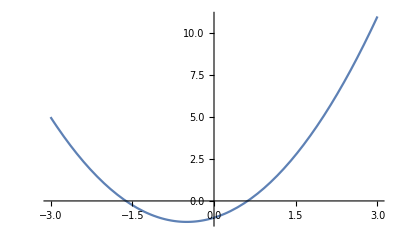

```mathematica
Plot[z^2+z-1,{z,-3,3}]
```

```mathematica
x^2+y^2-(z/2)^2-(p-{x,y,z}).v
```

-0.5+x+x^2+y^2+0.2 z-z^2/4

```mathematica
ContourPlot3D[-0.5+x+x^2+y^2+0.2 z-z^2/4,{x,-1,1},{y,-1,1},{z,-2,2}]
```

-Graphics3D-

```mathematica
sol=Solve[x^2+y^2+z^2==1&&x^3+x y^2==z^2,{x,y},Reals]
```

{{x→ConditionalExpression[-z^2/(-1+z^2), ],y→ConditionalExpression[-√(1-z^2-z^4/((-1+z^2)^2)), ]},{x→ConditionalExpression[-z^2/(-1+z^2), ],y→ConditionalExpression[√(1-z^2-z^4/((-1+z^2)^2)), ]}}

```mathematica
文件操作
```